# 2

## PHAS2443: Practical Mathematics II Lecture 2: Cellular Automata and Images

This lecture looks at the way the evolution of simple systems can produce complex patterns, and also the way in which very simple models based on particles can mimic some physical systems. It also includes a brief introduction to some techniques of image analysis.

## Cellular Automata

A cellular automaton is a system in which space is divided into discrete cells, and simple rules are used to derive the state of the system at any time step from the state at the previous step. The system may involve one or more spatial dimensions, and the rules may involve various numbers of neighbours to each cell. Although Mathematica includes a function, CellularAutomaton, to carry out the evolution, it is instructive to set up our own functions.

It is worth mentioning that the richness of cellular automata has links to the basic computational concept of the Turing Machine. Alan Turing introduced the abstract idea of a computer with a single read head that can be in a number of different states and a tape of coloured cells. The state of the head and the colour of the cell under it dictate what should happen next: for example, change the colour of the cell and move one space along the tape. Alex Smith, a 20-year-old student at Birmingham, proved in 2007 that a Turing machine with a two-state head and three-colour tape acts as a universal computer. In so doing he proved a conjecture of Stephen Wolfram's based on his explorations of cellular automata in his book A New Kind of Science.

### Simple One-Dimensional Automata

A basic cellular automaton has cells that can take on one of k possible values, 0, 1, 2,...(k-1).  If each cell's behaviour is determined by (2r+1) cells, that is, for cell number i a chunk of cells running from i-r to i+r is involved, then the total number of possible configurations of the chunk of cells is k^(2r+1), and as the update rule can apply any one of k values to each of those configurations the total number of rules is k^(k^(2r+1)), a very rapidly increasing function of k and r. Even if each cell can only take two values, 0 or 1, and the range r is restricted to 1, there are 256 possible rules.  We shall limit ourselves to that case for the moment.

Let us define a rule by specifying, for each pattern of 0s and 1s, the resulting value of the cell. For example

```mathematica
rule={{0,0,0}->0,{0,0,1}->1,{0,1,0}->1,{1,0,0}->0,{1,1,0}->1,{1,0,1}->1,{0,1,1}->1,{1,1,1}->0};
```

We could then set up an update procedure by the following procedure

```mathematica
upd[row_,rule_]:=Transpose[{RotateRight[row],row,RotateLeft[row]}]/.rule
```

```mathematica
ss=RandomInteger[{0,1},20]
upd[ss,rule]
```

{0,0,1,0,1,1,0,1,0,0,1,0,0,0,0,1,0,1,1,0}

{0,1,1,1,1,1,1,1,0,1,1,0,0,0,1,1,1,1,1,0}

```mathematica
ss=RandomInteger[{0,1},1000];
vv=NestList[upd[#1,rule]&,ss,500];
ListDensityPlot[vv,Mesh->False]
```

-Graphics-

```mathematica
rule={{0,0,0}->0,{0,0,1}->1,{0,1,0}->1,{1,0,0}->1,{1,1,0}->1,{1,0,1}->1,{0,1,1}->1,{1,1,1}->0};
ss=RandomInteger[{0,1},400];
Timing[vv=NestList[upd[#1,rule]&,ss,400];]
ListDensityPlot[vv,Mesh->False]
```

{0.292725,Null}

-Graphics-

The pattern generated here is very similar to the patterns found on shells of marine creatures, for example.

### Convolution

The process of 'sliding' a template over the row is similar to the process of convolution.
This animation is by Eric W. Weisstein (August 18, 2008), and this part of the notebook was downloaded from http://mathworld.wolfram.com/notebooks/IntegralTransforms/Convolution.nb.  For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/Convolution.html.

Here is an example of the general form of a convolution as implemented in Mathematica.

```mathematica
ListConvolve[{k1,k2,k3},{l1,l2,l3,l4},2,{0,0},g,h]
```

{h[g[k3,0],g[k2,l1],g[k1,l2]],h[g[k3,l1],g[k2,l2],g[k1,l3]],h[g[k3,l2],g[k2,l3],g[k1,l4]],h[g[k3,l3],g[k2,l4],g[k1,0]]}

The first argument of ListConvolve is the 'kernel', which is moved along the row. By default, the functions represented by g and h are Times and Plus respectively:

```mathematica
ListConvolve[{k1,k2,k3},{l1,l2,l3,l4},2,{0,0}]
```

{k2 l1+k1 l2,k3 l1+k2 l2+k1 l3,k3 l2+k2 l3+k1 l4,k3 l3+k2 l4}

The third argument, 2, controls the alignment of the kernel with the data list. The fourth argument, {0,0}, says that the data list will be padded at each end with 0s when the kernel overlaps the end of the list.

Now let's try to use ListConvolve to implement the cellular automaton. We'll need to define two functions, to put in the places of g and h. First, convert the rule into a set of functions:

```mathematica
ff=(rule/.({a_,b_,c_}->fup[a,b,c]))/.Rule->Set
```

{0,1,1,1,1,1,1,0}

We also need a function which, when passed the entry from the kernel and the entry from the data list, just returns the entry from the data list.

```mathematica
id[a_,b_]:=b
```

Now we can define a new update rule.

```mathematica
upd2[row_]:=ListConvolve[{1,1,1},row,2,{0,0},id,fup]
```

```mathematica
ss=RandomInteger[{0,1},400];
Timing[vv=NestList[upd2,ss,400];]
ListDensityPlot[vv,Mesh->False]
```

{1.13267,Null}

-Graphics-

That was less efficient than the previous method. It was not just that Mathematica had to scan several function definitions. The array restructuring operations that we used before are coded very efficiently in Mathematica.

## Two-Dimensional Cellular Automata

Two-dimensional cellular automata have been used in applications ranging from the simulation of forest fires through the spreading of disease to the behaviour of fluids. The best-known example is probably John Horton Conway's Game of Life, which shows an astonishing richness of behaviour arising from a simple set of rules. Here, we shall just show a simple example of diffusion behaviour. This application is rather different from the one above, as we apply a probability factor to decide whether or not a particle will diffuse. 
  This introduces a useful general idea. Suppose we want to execute some statement with a probability p. If we inagine a line from 0 to 1, if we split it into lengths p and (1-p), then select a random number between 0 and 1, the probability that the random number lies between 0 and p is just p. 
  We shall set up a spike of material in a square lattice, and move the 'atoms' at random, moving each one with probability 5%.

```mathematica
dim=31;ptot=100000;
init=Table[0,{dim},{dim}];
init⟦Ceiling[dim/2],Ceiling[dim/2]⟧=ptot;
upd[init_List]:=Module[{ii,jj,kk,iii,jjj,qq,ll,lll},qq=Table[0,{i,Length[init]},{j,Length[init⟦1⟧]}];Do[If[init⟦ii,jj⟧>0,lll=init⟦ii,jj⟧;Do[If[RandomReal[]<0.05,kk=RandomInteger[{1,4}];iii=ii;jjj=jj;Which[kk==1,iii=Mod[ii,dim]+1,kk==2,iii=Mod[ii-2,dim]+1,kk==3,jjj=Mod[jj,dim]+1,kk==4,jjj=Mod[jj-2,dim]+1];qq⟦ii,jj⟧=qq⟦ii,jj⟧-1;qq⟦iii,jjj⟧=qq⟦iii,jjj⟧+1],{ll,1,lll}]],{ii,1,dim},{jj,1,dim}];init+qq]
Do[Do[init=upd[init],{i,1,30}];Print[ListPlot3D[init,PlotRange->All,Mesh->False]],{j,1,10}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«7 more identical outputs»

What is remarkable about this is that a system in which each particle only moves left, right, backwards and forwards has resulted in a distribution which is, to the eye, circularly symmetrical. Depending on the behaviour being modelled, it may be possible to achieve this sort of result on a square mesh or it may be necessary to move to a hexagonal mesh.

#### Further explanation

As this is the longest Mathematica code block we have encountered so far, here is a summary of what the different parts do.
dim = 31;            sets the size of the system, 31 cells square
ptot = 100000;  defines the number of particles
init = Table[0, {dim}, {dim}];  init [[i, j]] gives the number of particles at (i, j). We start with no particles anywhere ...
init⟦Ceiling[dim/2], Ceiling[dim/2]⟧ = ptot; ... except for ptot particles right at the centre
upd[init_List] :=   We define an update function which controls what happens at each ' tick of the clock' 
Module[{ii, jj, kk, iii, jjj, qq, ll, lll},  We have several working variables, local to the module
qq = Table[0, {i, Length[init]}, {j, Length[init⟦1⟧]}]; Make a new copy of the mesh, with zeroes everywhere, to record changes
Do[.., {ii, 1, dim}, {jj, 1, dim}]; Look at every cell
   If[init⟦ii, jj⟧ > 0, lll = init⟦ii, jj⟧;  If there are some particles in the cell then
    Do[..{ll, 1, lll}]]],  for every particle in the cell
                If[RandomReal[] < 0.05`, decide whether it is going to move (here, with probability 5%), and if so
             kk = RandomInteger[{1, 4}]; pick at random one of the directions (right, left, up,down)
                iii = ii; jjj = jj; 
             Which[kk == 1, iii = Mod[ii, dim] + 1, 
                   kk == 2, iii = Mod[ii - 2, dim] + 1, 
                   kk == 3, jjj = Mod[jj, dim] + 1, 
                   kk == 4, jjj = Mod[jj - 2, dim] + 1];  Set (ii,jj) to the position it will move to
                                qq⟦ii, jj⟧ = qq⟦ii, jj⟧ - 1; 
              qq⟦iii, jjj⟧ = qq⟦iii, jjj⟧ + 1; save the changes in particle number in these cells
    init + qq  apply those changes -- that's the end of the module.
 Now use it:
Do[Do[init = upd[init], {i, 1, 30}];   apply the update rule 30 times
    Print[ListPlot3D[init, PlotRange → All, Mesh → False]],  plot the result
   {j, 1, 10}] and repeat 10 times.
   
   The Mod function conserves particles by making any particle that diffuses out of the right reappear on the left, and so on.

## Simple Examples of Image Manipulation

Let us set up a simple image containing three shapes and some random noise.

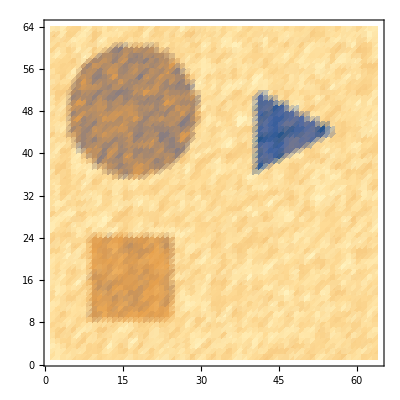

```mathematica
tr[x_,y_]:=If[y>0.5&&y<2 x&&y<3-2 x,1,0]
sq[x_,y_]:=If[x>-1.5&&x<-0.5&&y>-1.5&&y<-0.5,1,0]
circ[x_,y_]:=If[√((x-1)^2+(y+1)^2)<0.8,1,0]
im=Table[Floor[64-30 tr[x,y]-15 sq[x,y]-20 circ[x,y]+5 RandomReal[{-1,1}]],{x,-2,2,4/63},{y,-2,2,4/63}];
ListDensityPlot[im,Mesh->False]
```

### Edge Location

Now suppose we want to find the edges of these shapes. We want to know where the gradient of the data is large. One way of doing this is by taking differences. If we try this on a one-dimensional example we can see how well it works. Try a sine wave.

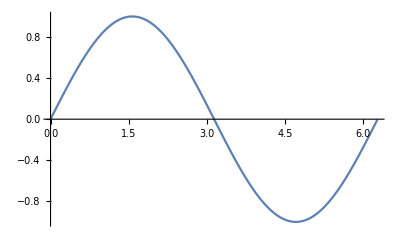

```mathematica
del=0.01;
ss=Table[{x,Sin[x]},{x,0,2 π,del}];
ListPlot[ss,Joined->True]
```

Now we can approximate the gradient at the point x by taking the difference:
dy/dx≈(y(x+dx)-y(x))/dx,
and we want to 'sweep' this differencing through the list of values. There are several ways of doing this, but perhaps the neatest are by using the Rotate function, or by convolution. 
  Consider Rotating the list: RotateLeft will convert {y1,y2,y3...yn} into {y2,y3,y4,...yn,y1}, and if we then subtract the original list from the rotated one we will have {y2-y1,y3-y2,y4-y3,...yn-y1} which, with the exception of the last entry, is what we want.

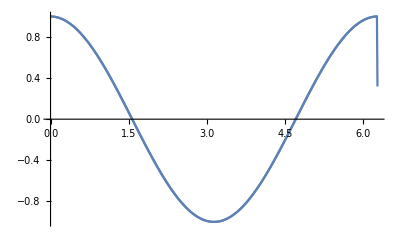

```mathematica
{ssx,ssy}=Transpose[ss];
ssd=(RotateLeft[ssy]-ssy)/del;
p1=ListPlot[Transpose[{ssx,ssd}],Joined->True];
p2=Plot[Cos[x],{x,0,2 π}];
Show[p1,p2]
```

The approximation agrees very well, except at the end - point, with the exact derivative.

If we use ListConvolve we have one point to watch. Unless we pad the array, we will end up with a shorter list than we started with. To get round this, we also drop one entry from the list of x coordinates.

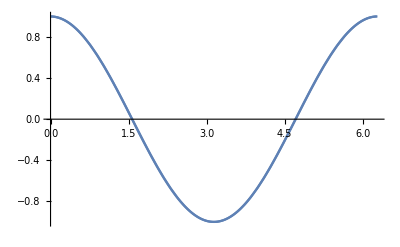

```mathematica
ssd=ListConvolve[{1/del,-1/del},ssy];p3=ListPlot[Transpose[{Drop[ssx,-1],ssd}],Joined->True];
Show[p2,p3]
```

#### Further Explanation

Let' s just take a moment to look at what ListConvolve[] does. We’ll set up a simple case, keeping everything as formulae rather than numbers:

```mathematica
ListConvolve[{1/d,-1/d},Array[y,6]]
```

{-y[1]/d+y[2]/d,-y[2]/d+y[3]/d,-y[3]/d+y[4]/d,-y[4]/d+y[5]/d,-y[5]/d+y[6]/d}

We can see that the convolution of the two - element kernel with the six - element data has resulted in a five - element list of results : the first item in the list is (y[2] - y[1])/d, which is the value we want to associate with the derivative at the first position. In this scheme we do not calculate a gradient to associate with the last element in the original list, which is why we drop the last value of x when we form the {x, dy/dx} list, using Drop[..., -1].

That’s the basic idea of applying so-called finite difference methods to calculating derivatives: we’ll explore it a bit more in the exercises for this lecture, and we’ll return to it later in the course. 
  Now apply this idea to the two-dimensional data array.This time we have to consider how to deal with the second dimension. Look carefully at what is being done to ensure you understand it. As we are just looking for changes, it doesn't matter whether we rotate left or right, and we want to pick up changes in both the horizontal and vertical directions.

{6.72732,Null}

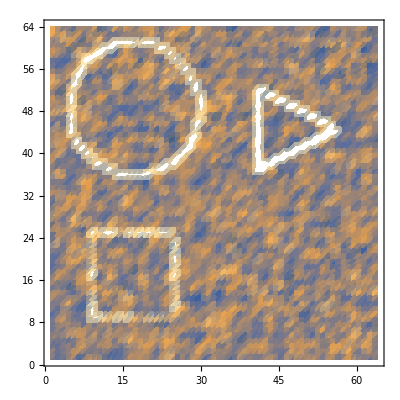

```mathematica
Timing[Do[diffim1=√((im-RotateRight[im])^2+(im-RotateRight/@im)^2),{i,1,100}];]
pim=ListDensityPlot[diffim1,Mesh->False]
```

We can tidy the result up with a threshold function:

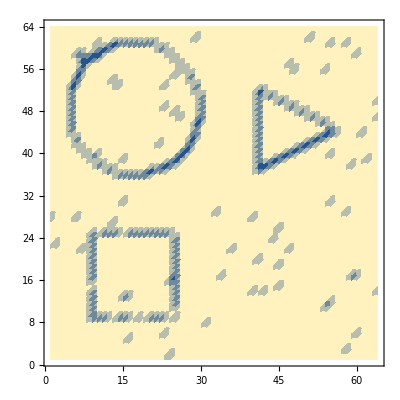

```mathematica
ListDensityPlot[Map[If[#>11,0,1]&,diffim1,{2}],Mesh->False]
```

{4.77393,Null}

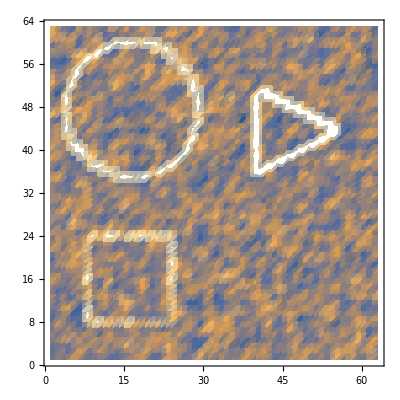

```mathematica
Timing[Do[diffim2=Sqrt[ListConvolve[{{-1,1},{0,0}},im]^2+ListConvolve[{{0,-1},{0,1}},im]^2],{i,1,100}];]
ListDensityPlot[diffim2,Mesh->False]
```

It looks as if the convolution is slightly more efficient than the Rotate method for a 2D situation.

There are many more sophisticated techniques for finding edges in images, as well as methods for modifying images by 'eroding' them to reduce them to skeletons which may be easier to recognise. This sort of technique is sometimes used in character recognition.

### Blurring of Images

The convolution operation can also be used to blur an image. In essence, blurring means that any point on an image receives a certain amount of the intensity that was intended for neighbouring points. A typical blurring function might be

```mathematica
blur=1/(x^2+y^2+5.);
blurt=Table[blur,{x,-10,10},{y,-10,10}];
Plot3D[blur,{x,-10,10},{y,-10,10},PlotRange->All]
```

-Graphics3D-

Let's see what this does to our image. We'll pad the image with zeros before convolving the blur function with it.

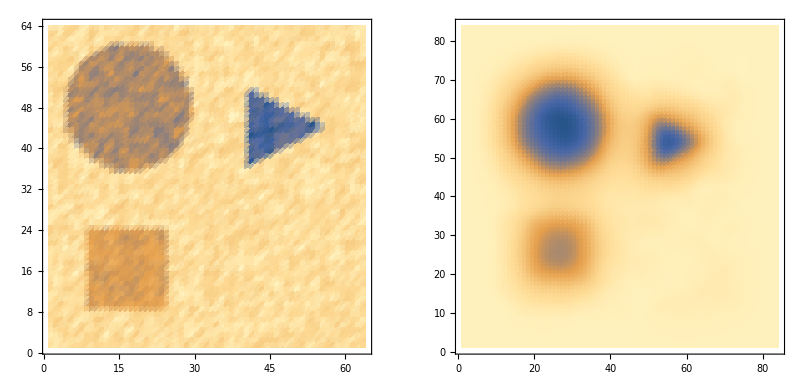

```mathematica
Show[GraphicsRow[{ListDensityPlot[im,Mesh->False],ListDensityPlot[ListConvolve[blurt,im,{1,-1},{64}],Mesh->False,PlotRange->All]}]]
```

Of course, what we have just done is what Nature does through diffraction effects or other features of optical systems. There are ways of 'undoing' this blurring, but we'll leave this for one of the mini-projects on the course.

## Summary

The main ideas that need to be carried forward from this lecture are the ways in which operations can be applied to lists or arrays of data. The methods for approximating differentials by rotating lists or by convolving a kernel with the list will be used when we come to study numerical methods for solving differential equations..

A.H. Harker
Physics and Astronomy, UCL
September 2005; updated January 2009, January 2010, January 2011.
Amended by Patrick Guio, Physics and Astronomy, January 2015 and January 2017.